1

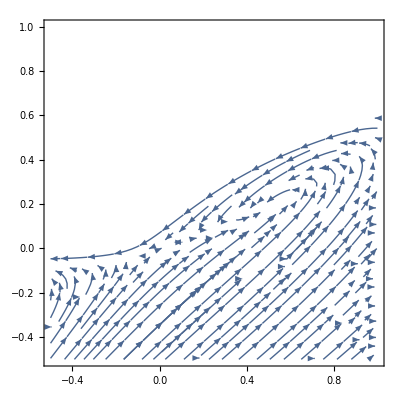

```mathematica
r=1
Block[{x,y},StreamPlot[{Sqrt[1+2x-5y]-1,ArcTan[x/2+3/5 x^2-2y]},{x,-1/2,1},{y,-1/2,1},StreamPoints->Fine]]
```

```mathematica
Solve[x^2-x-2==0,x]
```

{{x→-1},{x→2}}

```mathematica
ClearAll[x,y,u,v]
x:=u+1/2
y:=v+1/5
Series[Sqrt[1+2x-5y]-1,{u,0,1},{v,0,1}]
Series[ArcTan[x/2+3/5 x^2-2y],{u,0,1},{v,0,1}]
```

(-(5 v)/2+O[v]^2)+(1+(5 v)/2+O[v]^2) u+O[u]^2

(-2 v+O[v]^2)+(11/10+O[v]^2) u+O[u]^2